# Lecture 6: Numerical Strategy

## Battlecode Model Implemented in Mathematica:

```mathematica
nextTurnResources[numberOfBots_, bytecodeUsage_, currentResources_, decayMultiplier_: .8] := Module[{},
   currentResources*decayMultiplier - numberOfBots*(1 + bytecodeUsage/10000) + 40
   ];
buildMoreBots[howOften_] := (
  If[(round - howOften >= lastBotBuiltRound) && round > 0, lastBotBuiltRound = round; numberOfBots = numberOfBots + 1];
  myResources[[round + 1]] = nextTurnResources[numberOfBots, bytecodeUsage, myResources[[round]], decayMultiplier];
  )
killExcessBots[] := If[myResources[[round + 1]] < 0, numberOfBots = numberOfBots - 1];
generatorBonus[buildHowOften_, round_] := (
  (*get additional resources from generators*)
  myResources[[round]] = myResources[[round]] + 10*generatorNumber;
  If[(Mod[round, Floor@buildHowOften] == 0)
    && myResources[[round]] > 20*(encampmentCount + 1)
    && round < (Length@generators - 50)
   , myResources[[round]] = myResources[[round]] - 20*(encampmentCount + 1);
   generators[[round + 50]] = 1;
   encampmentCount++;
   ];
  generatorNumber = generatorNumber + generators[[round]];
  )
supplierBonus[buildHowOften_, round_] := (
  (*build encampments*)
  If[(Mod[round, Floor@buildHowOften] == 0)
    && myResources[[round]] > 20*(encampmentCount + 1)
    && round < (Length@generators - 50)
   , myResources[[round]] = myResources[[round]] - 20*(encampmentCount + 1);
   suppliers[[round + 50]] = 1;
   encampmentCount++;
   ];
  supplierNumber = supplierNumber + suppliers[[round]];
  spawnTime = 10*(10/(10 + supplierNumber));
  )

battlecodeModel[numRounds_, decayMultiplier_, bytecodeUsage_, generatorBuiltRounds_, supplierBuiltRounds_] := Module[{},
  myResources = ConstantArray[0, numRounds];
  generators = ConstantArray[0, numRounds];
  suppliers = ConstantArray[0, numRounds];
  numberOfBots = 0;
  generatorNumber = 0;
  supplierNumber = 0;
  encampmentCount = generatorNumber + supplierNumber;
  spawnTime = 10;
  lastBotBuiltRound = -1000;
  botCount = Table[
    generatorBonus[generatorBuiltRounds, round];
    supplierBonus[supplierBuiltRounds, round];
    buildMoreBots[spawnTime];
    killExcessBots[];
    numberOfBots
    , {round, 1, numRounds - 1}];
  Return@plotResults[]
  ]
plotResults[] := Module[{},
  plotOptions = {PlotRange -> All, AspectRatio -> 1/3, ImagePadding -> 20 {{1.5, 3}, {1, 1}}, ImageSize -> {600, 200}, PlotStyle -> Thick, BaseStyle -> {FontFamily -> "Calibri", FontSize -> 14}};
  generatorsAndSuppliers = ListPlot[{generators, suppliers}*{.8, .6}*Max@myResources, PlotStyle -> {Red, Black}];
  Return@{
    Show[ListLinePlot[myResources, plotOptions, AxesLabel -> {"Round", "Power"}], generatorsAndSuppliers]
    , ListLinePlot[botCount, plotOptions, AxesLabel -> {"Round", "# Robots"}]
    , Row[{Max@botCount
      , " Robots at round "
      , Position[botCount, Max@botCount][[1, 1]]
      , "."}, BaseStyle -> {FontFamily -> "Calibri", FontSize -> 14}]
    , ListLinePlot[Differences@Flatten@Position[Differences@botCount, 1], plotOptions[[2 ;;]], AxesLabel -> {"Round", "Spawn Time"}
     , PlotRange -> {Automatic, {0, 11}}]}
  ]
```

# Model usage

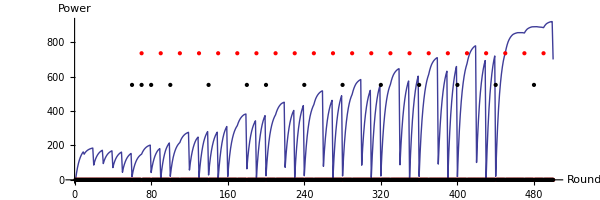
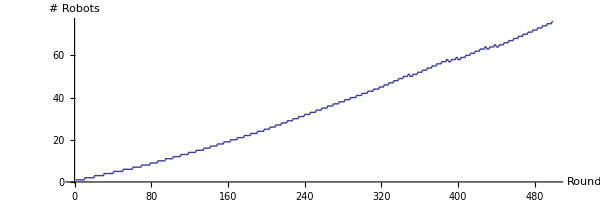
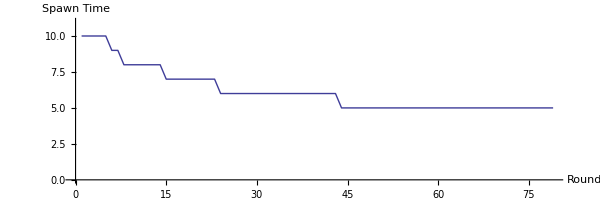
-Graphics-
-Graphics-
76 Robots at round 498.
-Graphics-

```mathematica
Column@battlecodeModel[
numberOfRounds = 500
,decayMultiplier =.8
,bytecodeUsage =0
,generatorBuiltRounds = 20
,supplierBuiltRounds =10
]
```

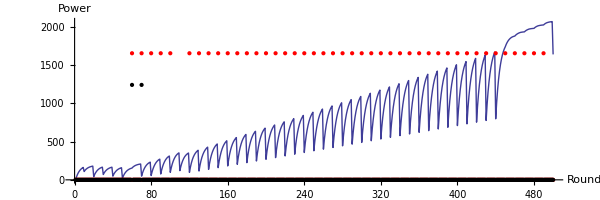
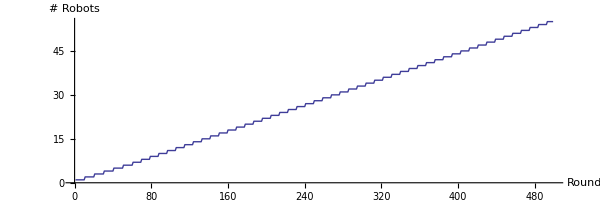
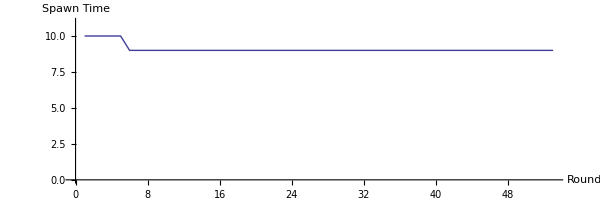
-Graphics-
-Graphics-
55 Robots at round 493.
-Graphics-

```mathematica
Column@battlecodeModel[
numberOfRounds = 500
,decayMultiplier =.8
,bytecodeUsage =0
,generatorBuiltRounds = 10(*Red*)
,supplierBuiltRounds =10(*Black*)
]
```

Production ability of HQ? 		40HP/(10 to 5)= 			4 to 8 HP/turn
Production ability of medbay? 		2*8 units				16 HP/turn
Killing ability of Artillery? 		(40 to 40+20*8=200)/20 turns = 	2 to 10 HP/turn

# Try an explicit build order

```mathematica
generatorBonus[round_,tryToBuild_]:= (
(*get additional resources from generators*)
myResources[[round]] = myResources[[round]]+10*generatorNumber;
If[(tryToBuild)
&&myResources[[round]]>20*(encampmentCount+1)+numberOfBots
&&round<(Length@generators-50)
,
myResources[[round]]=myResources[[round]]-20*(encampmentCount+1);
generators[[round+50]]=1;
current++;(*advance build order*)
encampmentCount++;
];
generatorNumber = generatorNumber+generators[[round]];
)
supplierBonus[round_,tryToBuild_]:= (
(*build encampments*)
If[(tryToBuild)
&&myResources[[round]]>20*(encampmentCount+1)+numberOfBots
&&round<(Length@generators-50)
,
myResources[[round]]=myResources[[round]]-20*(encampmentCount+1);
suppliers[[round+50]]=1;
current++;(*advance build order*)
encampmentCount++;
];
supplierNumber= supplierNumber+suppliers[[round]];
spawnTime = 10*(10/(10+supplierNumber));
)

battlecodeModelExplicit[numRounds_,decayMultiplier_,bytecodeUsage_,buildOrderIn_]:= Module[{buildOrder = buildOrderIn},
myResources = ConstantArray[0,numRounds];
generators = ConstantArray[0,numRounds];
suppliers = ConstantArray[0,numRounds];
numberOfBots = 0;
generatorNumber = 0;
supplierNumber = 0;
encampmentCount = generatorNumber+supplierNumber;
spawnTime = 10;
lastBotBuiltRound = -1000;
current = 1;
botCount = Table[
buildGenerator =False;buildSupplier = False;
If[current≤ Length@buildOrder,
If[buildOrder[[current]]==1,buildGenerator = True];
If[buildOrder[[current]] ==2,buildSupplier = True];
If[buildOrder[[current]] ==0,current++];
If[buildOrder[[current]]<0,buildOrder[[current]]++];(*allows a delay to be specified as a negative number*)
];
generatorBonus[round,buildGenerator];
supplierBonus[round,buildSupplier];
buildMoreBots[spawnTime];
killExcessBots[];
numberOfBots
,{round,1,numRounds-1}];
Return@plotResults[]
]
```

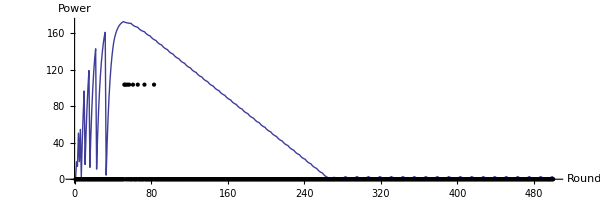
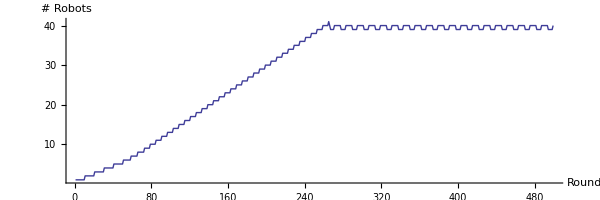
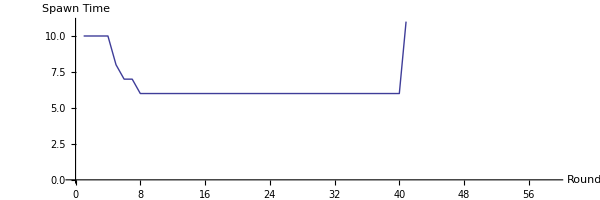
-Graphics-
-Graphics-
41 Robots at round 265.
-Graphics-

```mathematica
Column@battlecodeModelExplicit[
numberOfRounds = 500
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{{2,2,2,2,2,2,2,2},ConstantArray[{1},200]}
]
```

# Let’s explore the space

## Start with suppliers then generators

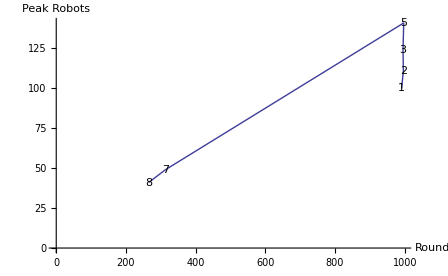

```mathematica
strategyExploration = Table[
{i,battlecodeModelExplicit[
numberOfRounds = 1000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[2,i],ConstantArray[1,200]}
][[3,1,{1,3}]]}
,{i,1,10}];
simplifiedExploration =Union[strategyExploration,SameTest-> (Round[#1[[2]],10]==Round[#2[[2]],10]&)];
r1 =Show[ListLinePlot[
Reverse/@simplifiedExploration[[;;,2]]
,AxesOrigin-> {0,0},AxesLabel-> {"Round","Peak Robots"}]
,Graphics[MapThread[Text[#1,Reverse@#2,{0,0}]&,Transpose@simplifiedExploration]],BaseStyle-> 16,PlotRangePadding-> {{0,20},{0,10}}]
```

## Let’s consider switching from all suppliers to a mix

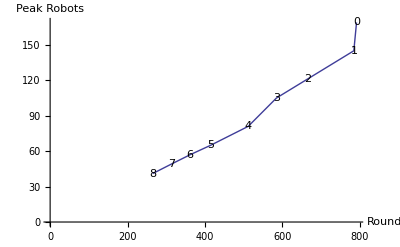

```mathematica
strategyExploration = Table[
{i,battlecodeModelExplicit[
numberOfRounds =1000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[2,i],ConstantArray[{1,2},200]}
][[3,1,{1,3}]]}
,{i,0,10}];
simplifiedExploration =Union[strategyExploration,SameTest-> (Round[#1[[2]],10]==Round[#2[[2]],10]&)];
r2 = Show[ListLinePlot[
Reverse/@simplifiedExploration[[;;,2]]
,AxesOrigin-> {0,0},AxesLabel-> {"Round","Peak Robots"}]
,Graphics[MapThread[Text[#1,Reverse@#2,{0,0}]&,Transpose@simplifiedExploration]],BaseStyle-> 16,PlotRangePadding-> {{0,20},{0,10}}]
```

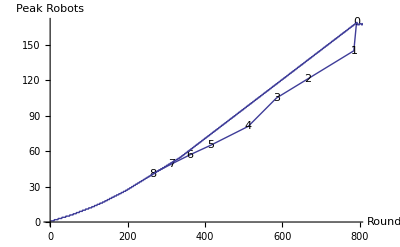

```mathematica
Show[r2,
battlecodeModelExplicit[
numberOfRounds =1000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[2,0],ConstantArray[{1,2},200]}
][[2]]
]
```

## So we see that it is always better to use a zero!

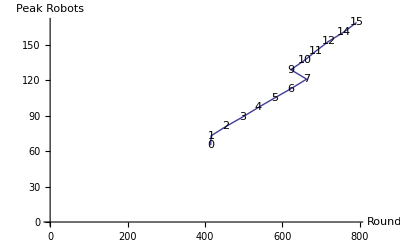

```mathematica
strategyExploration = Table[
{i,battlecodeModelExplicit[
numberOfRounds =2000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[{1,2},i],ConstantArray[{1,2,2,2},200]}
][[3,1,{1,3}]]}
,{i,0,20}];
simplifiedExploration =Union[strategyExploration,SameTest-> (Round[#1[[2]],10]==Round[#2[[2]],10]&)];
r3 = Show[ListLinePlot[
Reverse/@simplifiedExploration[[;;,2]]
,AxesOrigin-> {0,0},AxesLabel-> {"Round","Peak Robots"}]
,Graphics[MapThread[Text[#1,Reverse@#2,{0,0}]&,Transpose@simplifiedExploration]],BaseStyle-> 16,PlotRangePadding-> {{0,20},{0,10}}]
```

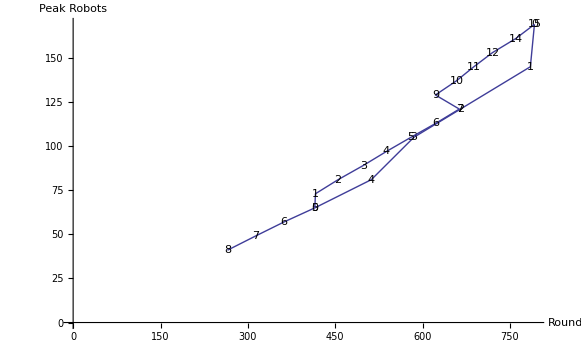

```mathematica
Show[r2,r3]
```

## Let’s try starting with generators, then building suppliers

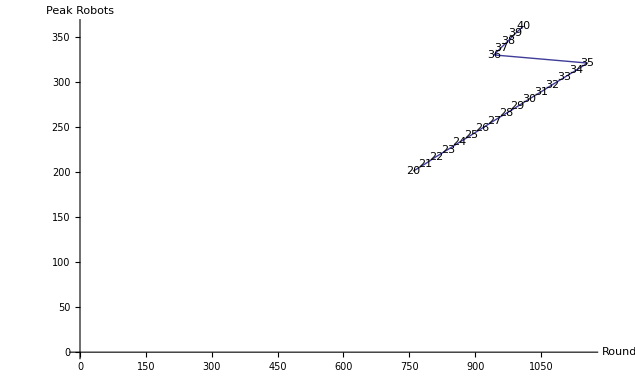

```mathematica
strategyExploration = Table[
{i,battlecodeModelExplicit[
numberOfRounds =2000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[1,i],ConstantArray[2,200]}
][[3,1,{1,3}]]}
,{i,20,40}];
simplifiedExploration =Union[strategyExploration,SameTest-> (Round[#1[[2]],10]==Round[#2[[2]],10]&)];
g1 = Show[ListLinePlot[
Reverse/@simplifiedExploration[[;;,2]]
,AxesOrigin-> {0,0},AxesLabel-> {"Round","Peak Robots"}]
,Graphics[MapThread[Text[#1,Reverse@#2,{0,0}]&,Transpose@simplifiedExploration]],BaseStyle-> 16,PlotRangePadding-> {{0,20},{0,10}}]
```

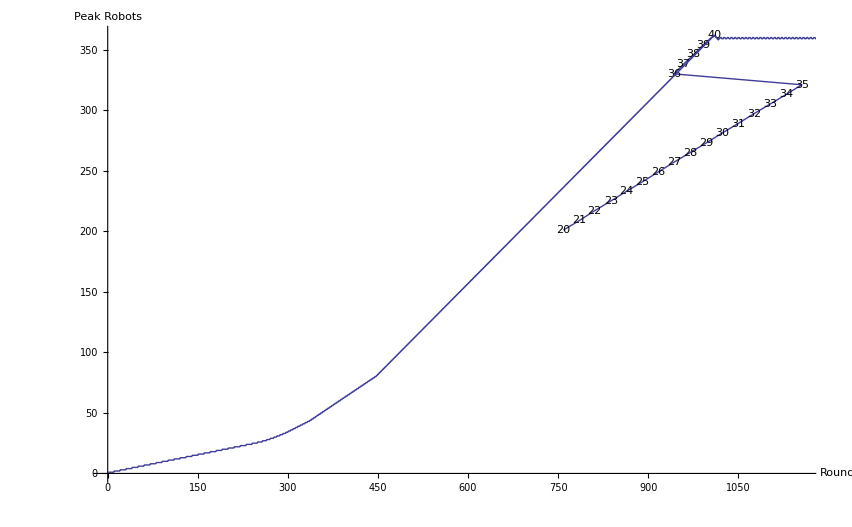

```mathematica
Show[g1
,battlecodeModelExplicit[
numberOfRounds =2000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[1,40],ConstantArray[2,200]}
][[2]]
]
```

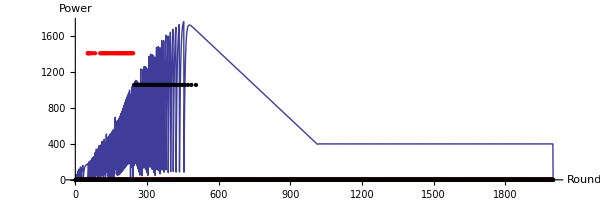
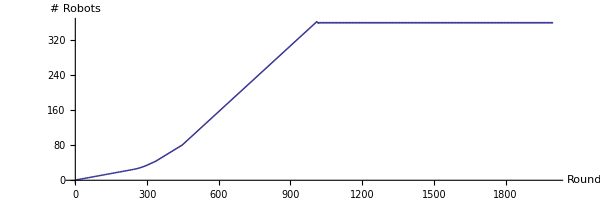
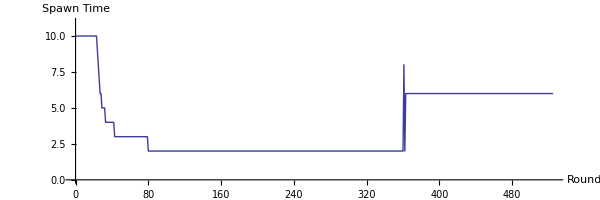
{-Graphics-,-Graphics-,362 Robots at round 1010.,-Graphics-}

```mathematica
battlecodeModelExplicit[
numberOfRounds =2000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[1,40],ConstantArray[2,200]}
]
```

## What about late game?

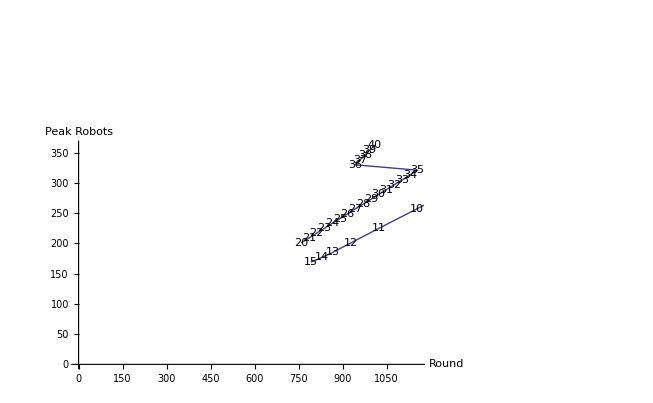

```mathematica
strategyExploration = Table[
{i,battlecodeModelExplicit[
numberOfRounds =2000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[{1,2},i],ConstantArray[{1,1,2},200]}
][[3,1,{1,3}]]}
,{i,0,20}];
simplifiedExploration =Union[strategyExploration,SameTest-> (Round[#1[[2]],10]==Round[#2[[2]],10]&)];
r4 = Show[ListLinePlot[
Reverse/@simplifiedExploration[[;;,2]]
,AxesOrigin-> {0,0},AxesLabel-> {"Round","Peak Robots"}]
,Graphics[MapThread[Text[#1,Reverse@#2,{0,0}]&,Transpose@simplifiedExploration]],BaseStyle-> 16,PlotRangePadding-> {{0,20},{0,10}}];
Show[g1,r4]
```

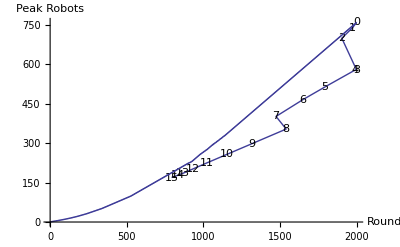

```mathematica
Show[r4,
battlecodeModelExplicit[
numberOfRounds =2000
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[{1,2},0],ConstantArray[{1,1,2},200]}
][[2]]
]
```

## What about a rush?

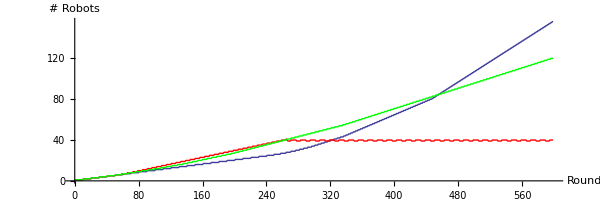

```mathematica
Show[
battlecodeModelExplicit[
numberOfRounds =600
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[1,40],ConstantArray[2,200]}
][[2]]
,(battlecodeModelExplicit[
numberOfRounds =600
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[2,40],ConstantArray[1,200]}
][[2]]/.Thick-> Directive[{Thick,Red}])
,(battlecodeModelExplicit[
numberOfRounds =600
,decayMultiplier =.8
,bytecodeUsage =0
,Flatten@{ConstantArray[{1,2},40],ConstantArray[1,200]}
][[2]]/.Thick-> Directive[{Thick,Green}])
]
```

# Encounters of units

## Let’s assume they all are dealing damage

The first units deal damage equally
the next ones deal damage to one unit, going along

```mathematica
team1Units = 10;(*make sure this number is less than team 2 units*)
team2Units = 10;
team1hp = ConstantArray[40,team1Units];
team2hp = ConstantArray[40,team2Units];
```

```mathematica
getNextHP[]:= (
team2hp[[;;team1Units]] = team2hp[[;;team1Units]]-6;
team1hp[[;;]] = team1hp[[;;]]-6;
remainingUnits = Min[team2Units-team1Units,team1Units];
team1hp[[;;remainingUnits]]= team1hp[[;;remainingUnits]]-6;
(*now reduce the number of units*)
team1hp = Select[team1hp,#>0&];
team1Units = Length@team1hp;
team2hp = Select[team2hp,#>0&];
team2Units = Length@team2hp;
)
```

```mathematica
simulateCombat[team1UnitsIn_,team2UnitsIn_]:= Module[{t},
team1Units = team1UnitsIn;
team2Units = team2UnitsIn;
(*team1Units = 10;(*make sure this number is less than team 2 units*)
team2Units = 11;*)
team1hp = ConstantArray[40,team1Units];
team2hp = ConstantArray[40,team2Units];
(*Print@Dynamic@team1hp;
Print@Dynamic@team2hp;*)
While[team1Units>0,
getNextHP[];
(*Pause[0];*)
];
unitKillRatio = team1UnitsIn/Max[(team2UnitsIn-team2Units),.001];
hpKillRatio = team1UnitsIn*40/Max[(team2UnitsIn*40-Total@team2hp),.001];
Return@{{"Robot Kill Ratio",N@unitKillRatio},{"HP Kill Ratio",N@hpKillRatio}}
]
```

```mathematica
TableForm@simulateCombat[10,11]
```

Robot Kill Ratio | 1.42857
HP Kill Ratio | 1.06383

# Let’s look at a lot of results

```mathematica
combatResults = Table[
Flatten[{N@i/20,simulateCombat[20,i][[;;,2]]}]
,{i,21,50}];
Style[TableForm[Join[{{"Force Ratio","Unit Kill Ratio","HP Kill Ratio"}},
combatResults
]],FontSize-> 14,FontFamily-> "Calibri"
]
```

Force Ratio | Unit Kill Ratio | HP Kill Ratio
1.05 | 1.17647 | 1.03093
1.1 | 1.42857 | 1.06383
1.15 | 1.81818 | 1.0989
1.2 | 2.5 | 1.13636
1.25 | 4. | 1.17647
1.3 | 10. | 1.21951
1.35 | 20000. | 1.25786
1.4 | 20000. | 1.28205
1.45 | 20000. | 1.30719
1.5 | 20000. | 1.33333
1.55 | 20000. | 1.36054
1.6 | 20000. | 1.38889
1.65 | 20000. | 1.41844
1.7 | 20000. | 1.44928
1.75 | 20000. | 1.48148
1.8 | 20000. | 1.51515
1.85 | 20000. | 1.55039
1.9 | 20000. | 1.5873
1.95 | 20000. | 1.62602
2. | 20000. | 1.66667
2.05 | 20000. | 1.66667
2.1 | 20000. | 1.66667
2.15 | 20000. | 1.66667
2.2 | 20000. | 1.66667
2.25 | 20000. | 1.66667
2.3 | 20000. | 1.66667
2.35 | 20000. | 1.66667
2.4 | 20000. | 1.66667
2.45 | 20000. | 1.66667
2.5 | 20000. | 1.66667

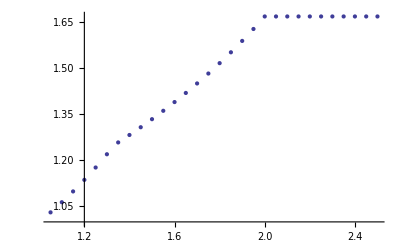

```mathematica
pts = ListPlot[combatResults[[;;,{1,3}]],PlotStyle-> Thick]
```

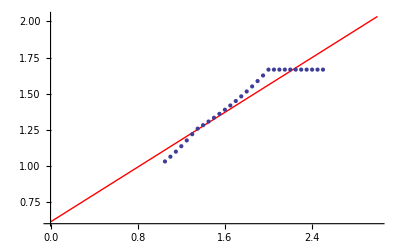

0.612418+0.474079 x

```mathematica
theline = a x + b/.FindFit[combatResults[[;;,{1,3}]],a x + b,{a,b},x];
Show[Plot[theline,{x,0,3},PlotStyle-> Red],pts]
theline
```

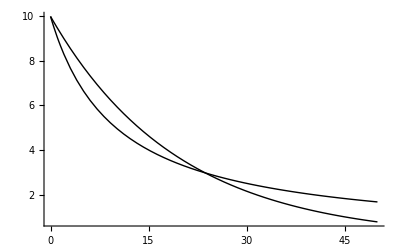

```mathematica
Plot[
(10{{.95^n},{(10/(10+n))}})
,{n,0,50},PlotRange-> All,PlotStyle-> {Red,Black},AxesOrigin-> {0,0}]
```